# Algorithmic Differentiation

We need first and second derivatives for our tests and algorithms.  In the real world our constraints and cost function are defined by computer code. Algorithmic Differentiation (AD) provides ways to generate code for derivatives from the code for the functions.  It used to be called Automatic Differentiation but the folks that do it thought that gave the wrong impression and just decided to change their name but not their acronym!

First a reminder of what we know.

## Derivatives and Finite Differences

For f:ℝ→ℝ and x∈ℝ
	f'[x]=lim_(h->0) (f[x+h]-f[x])/h

For f:ℝ^n→ℝ and and x,u∈ℝ^n
	∂_u f | = | lim_(h->0) (f[x+ h u ]-f[x])/h
(∂f)/(∂x_i) | = | lim_(h->0) (f[x+ h e_i ]-f[x])/h
Df | = | {∂_1 f,∂_2 f,…,∂_n f}
where ∂_i f=∂f/∂x_i and we have skipped writing down the x dependence.

A derivative of a derivative is a second derivative.  The Hessian of  f:ℝ^n→ℝ 
is the n×n symmetric matrix of second derivatives
	(∂f)/(∂x_i∂x_j) | = | ∂_i (∂_j f) | = | ∂_j (∂_i f)
DDf_(i,j) | = | H_(i,j) | = | ∂_ij f  
Calculus courses usually cover finite Difference(FD) approximations

  | Forward Diff | Centered Diff
f'[x] | (f[x+h]-f[x])/h | (f[x+h]-f[x-h])/(2h)
f''[x] | (f[x+2h]-2f[x+h]+f[x])/h^2  | (f[x+h]-2f[x]+f[x-h])/h^2
∂_i f[x] | (f[x+he_i]-f[x])/h | (f[x+he_i]-f[x-he_i])/(2h)
∂_(i,j) f[x] | (f[x+he_i+ he_j]-f[x+he_i]- f[x+he_j]+ f[x])/h^2 | (f[x+he_i+ he_j]-f[x+he_i-he_j]- f[x+he_j-he_i]+ f[x-he_i-he_j])/h^2

Taylor Series (TS) show that centered differences are more accurate with error behavior described by the TS error terms.

```mathematica
f[x_]:= Cos[x + Exp[ Sin[Log[1+x^2]]]]
x=1.5;
SetOptions[LogLogPlot,GridLines->Automatic,MaxRecursion->4,Frame->True];
LogLogPlot[{
h,Abs[f'[x]-(f[x+h]-f[x])/h],Abs[f''[x]-(f[x+2h]-2f[x+h]+f[x])/h^2],
h^2,Abs[f'[x]-(f[x+h]-f[x-h])/(2h)],Abs[f''[x]-(f[x+h]-2f[x]+f[x-h])/h^2]
},{h,10^-9, 1},
FrameLabel->{"h","err"},
PlotLegends->{"O(h)","FD_1","FD_2","O(h^2)","CD_1","CD_2"}]
```

## Algorithmic Differentiation

Every single piece of a computer function is either arithmetic, logic, or a call to a special function that we  know the derivative of.  Each of those pieces (except the logic) is differentiable. So we can go line by line and differentiate.  At the bottom level this is all AD is.  There are two common ways to accumulate the derivatives.  Forward or Backward in the flow of the program.  Forward is easy to understand and code. Backwards is theoretically more efficient at computing the gradient of a function f:ℝ^n→ℝ.

### Basic Example: Forward Mode

This is much clearer with an example. The function from f:ℝ^3→ℝ^2
	f[x]={x_3+x_1 x_2,x_1 x_2+Cos[x_1+Sin[x_3]]}
is easy to implement.  Here is code to compute it in small steps with the work variables stored in a sequence of “work” variables.

```mathematica
f[{x1_,x2_,x3_}]:= Module[{w1,w2,w3,w4,w5},
w1=x1*x2;
w2=x3+w1;
w3=Sin[x3];
w4=x1+w3;
w5=Cos[w4];
{w2,w5}
]
```

Functions always need to be tested.  This is far from a complete test!

```mathematica
x={0.2,1.4,0.6};
f[x]
```

Here is a forward mode Algorithmic Differentiation (AD) code for the function.

```mathematica
df[{x1_,x2_,x3_},{dx1_,dx2_,dx3_}]:= Module[
{w1,w2,w3,w4,w5,dw1,dw2,dw3,dw4,dw5},

dw1=dx1*x2+x1*dx2;
w1=x1*x2;

dw2=dx3+dw1;
w2=x3+w1;

dw3=Cos[x3]*dx3;
w3=Sin[x3];

dw4=dx1+dw3;
w4=x1+w3;

dw5=-Sin[w4]*dw4;
w5=Cos[w4];

{{w2,w5},{dw2,dw5}}
]
```

We need to test this trick.

```mathematica
x={0.2,-0.4,-0.6};
dx={1.2,-3.6,-3.4};
{{f1,f2},{df1,df2}}=df[x,dx]
Plot[{f[x+ h dx]⟦1⟧,f[x+ h dx]⟦2⟧,
f1+h df1,f2+h df2},
{h, -0.5,0.5},
PlotLegends->{"f_1","f_2","t_1","t_2"}]
```

They look like tangent lines to me.   The AD code produces accurate derivatives!

```mathematica
n=3;
{x0,dx0}=RandomReal[{-1,1},{2,n}];
Gradf[{x1_,x2_,x3_}]=D[f[{x1,x2,x3}],{{x1,x2,x3}}];
Df0=Gradf[x0].dx0
{f0,df0}=df[x0,dx0]
Df0-df0
```

The centered difference produces reasonably accurate derivatives IF we use a good value for “h”.

```mathematica
LogLogPlot[{
h,h^2,
Norm[Df0-(f[x0+h dx0]-f[x0])/h],
Norm[Df0-(f[x0+h dx0]-f[x0-h dx0])/(2h)]
},{h, 10^-12, 1},
GridLines->Automatic,Frame->True,FrameLabel->{"h","err"},
PlotLegends->{"O(h)","O(h^2)","FD_err","CD_err"},
MaxRecursion->2]
```

### Multiple 1st Derivatives

You can do the several 1st derivative at the same time.  I am going to illustrate this on the generalized Rosenbrock function 
	f:ℝ^n→ℝ.
https://en.wikipedia.org/wiki/Rosenbrock_function.
Here is an AD implementation of the Rosenbrock function computing two directional first derivatives simultaneously.

```mathematica
Rosen[x_]:= Module[{n=Length[x],eta=100.0,sum=0.0},
Do[sum+=eta*(x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,
{i,1,n-1}];
sum]

dRosen[x_,{dx1_,dx2_}]:= Module[{n=Length[x],eta=100.0,sum=0.0,
(* Added Accumulators for 1st derivatives *)
dsum1=0.0,dsum2=0.0},
Do[
(* 1st derivative in the dx1 direction *)
dsum1+=2.0*eta*(x⟦i+1⟧-x⟦i⟧^2)*(dx1⟦i+1⟧-2.0x⟦i⟧*dx1⟦i⟧)-2.0*(1-x⟦i⟧)*dx1⟦i⟧;
(* 1st derivative in the dx2 direction *)
dsum2+=2.0*eta*(x⟦i+1⟧-x⟦i⟧^2)*(dx2⟦i+1⟧-2.0x⟦i⟧*dx2⟦i⟧)-2.0*(1.0-x⟦i⟧)*dx2⟦i⟧;
(* Original Code *)
sum+=eta*(x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,
{i,1,n-1}];
{sum,{dsum1,dsum2}}]
```

Here is a test.

```mathematica
n=12;
{x0,dx1,dx2}=RandomReal[{-1,1},{3,n}];
{f0,{df1,df2}}=dRosen[x0,{dx1,dx2}];
TabView[{
"3D"->Show[
Plot3D[{
Rosen[x0+h1 dx1 + h2 dx2],
f0+h1 df1 + h2 df2},
{h1, -0.5,0.5},{h2,-0.5,0.5}]
],
"3D-err"->Plot3D[Abs[f0+h1 df1 + h2 df2-Rosen[x0+h1 dx1 + h2 dx2]],
{h1, -0.5,0.5},{h2,-0.5,0.5}],
"LogLog-err"->LogLogPlot[{
h^2,
Abs[f0+h df1-Rosen[x0+h dx1]],
Abs[f0+h df2-Rosen[x0+h dx2]]},{h, 10^-11,0.5},
PlotLegends->{"O(h^2)","1","2"}]
},1]
```

123

### Second Derivatives

You can keep going to build second derivatives.  I am going to make sure I do not make algebraic mistakes this time. Since
	Rosen[x]=Sum[η (x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,{i,1,n-1}]
I can get Mathematica to build the expressions I need to get the second derivatives.

```mathematica
Clear[i,j,x,dx1,dx2]
sub:=x[[j_]]:>x[[j]]+h1 dx1[[j]]+h2 dx2⟦j⟧
Quiet[Normal[CoefficientArrays[(1-x⟦i⟧)^2/.sub,
{h1,h2},
Symmetric->True]]]
```

```mathematica
Clear[i,j,x,dx1,dx2]
sub:=x[[j_]]:>x[[j]]+h1 dx1[[j]]+h2 dx2⟦j⟧
Hmm=FullSimplify[
Quiet[Normal[CoefficientArrays[(x⟦i+1⟧-x⟦i⟧^2)^2/.sub,
{h1,h2},
Symmetric->True]]]];
Hmm⟦1⟧
Hmm⟦2⟧
Hmm⟦3,1,1⟧
Hmm⟦3,2,2⟧
Hmm⟦3,1,2⟧
```

dx1⟦1+i⟧ (dx2⟦1+i⟧-2 dx2⟦i⟧ x⟦i⟧)-2 dx1⟦i⟧ (dx2⟦1+i⟧ x⟦i⟧+dx2⟦i⟧ (-3 x⟦i⟧^2+x⟦1+i⟧))

```mathematica
ddRosen[x_,{dx1_,dx2_}]:= Module[{n=Length[x],eta=100.0,sum=0.0,
(* Added Accumulators for 1st derivatives *)
dsum1=0.0,dsum2=0.0,
(* Added Accumulators for 2nd derivatives *)
ddsum11=0.0,ddsum22=0.0,ddsum12=0.0},
Do[
(* 2nd derivative ∂_11 *)
ddsum11+=eta*(dx1⟦1+i⟧^2-4 dx1⟦i⟧ dx1⟦1+i⟧ x⟦i⟧+2 dx1⟦i⟧^2 (3 x⟦i⟧^2-x⟦1+i⟧))+dx1⟦i⟧^2;
(* 2nd derivative ∂_22 *)
ddsum22+=eta*(dx2⟦1+i⟧^2-4 dx2⟦i⟧ dx2⟦1+i⟧ x⟦i⟧+2 dx2⟦i⟧^2 (3 x⟦i⟧^2-x⟦1+i⟧))+dx2⟦i⟧^2;
(* 2nd derivative ∂_12=∂_21 *)
ddsum12+=eta*(
dx1⟦1+i⟧ (dx2⟦1+i⟧-2 dx2⟦i⟧ x⟦i⟧)-2 dx1⟦i⟧ (dx2⟦1+i⟧ x⟦i⟧+dx2⟦i⟧ (-3 x⟦i⟧^2+x⟦1+i⟧)))
+dx1⟦i⟧ dx2⟦i⟧;
(* 1st derivative in the dx1 direction *)
dsum1+=2.0*eta*(x⟦i+1⟧-x⟦i⟧^2)*(dx1⟦i+1⟧-2.0x⟦i⟧*dx1⟦i⟧)-2.0*(1-x⟦i⟧)*dx1⟦i⟧;
(* 1st derivative in the dx2 direction *)
dsum2+=2.0*eta*(x⟦i+1⟧-x⟦i⟧^2)*(dx2⟦i+1⟧-2.0x⟦i⟧*dx2⟦i⟧)-2.0*(1.0-x⟦i⟧)*dx2⟦i⟧;
(* Original Code *)
sum+=eta*(x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,
{i,1,n-1}];
{sum,{dsum1,dsum2},({{ddsum11, ddsum12}, {ddsum12, ddsum22}})}]
```

This is worth testing!

```mathematica
n=12;
{x0,dx1,dx2}=RandomReal[{-1,1},{3,n}];
{α,β}=Normalize[RandomReal[{-1,1},2]];
u=α dx1 + β dx2;
```

```mathematica
{f0,g,H}=ddRosen[x0,{dx1,dx2}];

TabView[{
"3D"->Show[
Plot3D[{
Rosen[x0+h1 dx1 + h2 dx2],
f0+g.{h1,h2} + 0.5 {h1,h2}.H.{h1,h2} },
{h1, -0.5,0.5},{h2,-0.5,0.5}]
],
"3D-err"->Plot3D[Abs[f0+g.{h1,h2} + 0.5 {h1,h2}.H.{h1,h2}-Rosen[x0+h1 dx1 + h2 dx2]],
{h1, -0.5,0.5},{h2,-0.5,0.5}],
"LogLog-err"->LogLogPlot[{
h^2,
Abs[f0+h g.{α,β} +0.5 h^2 {α,β}.H.{α,β} -Rosen[x0+h u]]
},{h, 10^-11,0.5},
PlotLegends->{"O(h^3)","1"}]
},1]
```

123

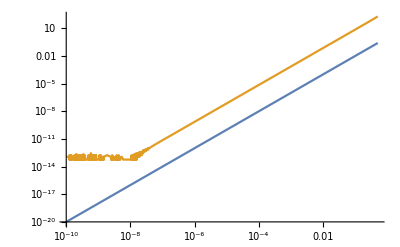

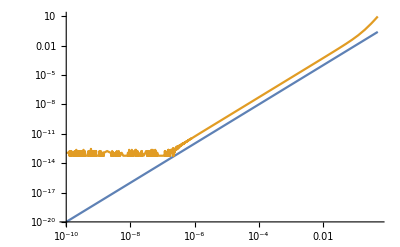

```mathematica
LogLogPlot[{h1^2,Abs[f0+h1 df1 - Rosen[x0+h1 dx1]]},{h1,10^-10,0.5}]
LogLogPlot[{h1^2,Abs[f0+h1 df1 +0.5 h1^2 df11- Rosen[x0+h1 dx1]]},{h1,10^-10,0.5}]
```

Here is code to computing the gradient “automatically” in Mathematica.

```mathematica
Clear[x]
vars=Array[x,n];
Quiet[
gradR[x_]=D[Rosen[vars],{vars}]/.x[i_]:>x⟦i⟧
];
```

Here is AD code computing the mixed derivative at the same time as the two directional derivatives.

```mathematica
ddRosen[x_,dx1_,dx2_]:= Module[{n=Length[x],eta=100.0,sum=0.0,
(* Added Accumulators for 1st derivatives *)
dsum1=0.0,dsum2=0.0,
(* Added Accumulators Mixed Second derivative *)
ddsum12=0.0},
Do[
(* Mixed second derivative *)
ddsum12+=
2.0*eta*(dx2⟦i+1⟧-2x⟦i⟧dx2⟦i⟧)*(dx1⟦i+1⟧-2.0x⟦i⟧*dx1⟦i⟧)+
2.0*eta*(x⟦i+1⟧-x⟦i⟧^2)*(0.0-2.0dx2⟦i⟧*dx1⟦i⟧)
-2.0*(0.0-dx2⟦i⟧)*dx1⟦i⟧;
(* derivatives in the dx1 and dx2 directions *)
dsum1+=2.0*eta*(x⟦i+1⟧-x⟦i⟧^2)*(dx1⟦i+1⟧-2.0x⟦i⟧*dx1⟦i⟧)-2.0*(1-x⟦i⟧)*dx1⟦i⟧;
dsum2+=2.0*eta*(x⟦i+1⟧-x⟦i⟧^2)*(dx2⟦i+1⟧-2.0x⟦i⟧*dx2⟦i⟧)-2.0*(1.0-x⟦i⟧)*dx2⟦i⟧;
(* Original Code *)
sum+=eta*(x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,
{i,1,n-1}];
{sum,{dsum1,dsum2}}]
```

Here is a test.

```mathematica
Plot[
dRosen[x0+h dx1,dx1,dx2]⟦2,1⟧
```

```mathematica
Plot[ dRosen[x0,dx1,dx2]]
```

```mathematica
ddf[{x1_,x2_,x3_},{dx1_,dx2_,dx3_},
{dy1_,dy2_,dy3_}]:= Module[
{w1,w2,w3,w4,w5,
dw1,dw2,dw3,dw4,dw5,
ddw1,ddw2,ddw3,ddw4,ddw5},

ddw1=dx1*dy2+dy1*dx2;
dw1=dx1*x2+x1*dx2;
w1=x1*x2;

ddw2=0.0+ddw1;
dw2=dx3+dw1;
w2=x3+w1;

ddw3=-Sin[x3]*dy3*dx3;
dw3=Cos[x3]*dx3;
w3=Sin[x3];

ddw4=0.0+ddw3;
dw4=dx1+dw3;
w4=x1+w3;

ddw5=-Cos[w4]*dw4*dw4-Sin[w4]*ddw4;
dw5=-Sin[w4]*dw4;
w5=Cos[w4];

{{w2,w5},{dw2,dw5},{ddw2,ddw5}}
]
```

```mathematica
Gradf[{x1_,x2_,x3_}]=D[f[{x1,x2,x3}],{{x1,x2,x3}}];
GradGradf[{x1_,x2_,x3_}]=D[f[{x1,x2,x3}],{{x1,x2,x3},2}];

x={0.2,-0.4,-0.6};
dx={1.2,-3.6,-3.4};
dy={-1.2,3.2,3.1};
{{f1,f2},{df1,df2},{ddf1,ddf2}}=ddf[x,dx,dy];
Gradf[x].dx-{df1,df2}
(GradGradf[x].dx).dy
D[Gradf[x+g dy].dx,g]/.g->0
```

```mathematica
{ddf1,ddf2}
```

```mathematica
Clear[h,g]
D[D[f[x+h dx + g dy],h],g]/.{h->0,g->0}
D[Gradf[x+ g dy].dx,g]/.g->0.0
{ddf1,ddf2}
```

```mathematica
Plot[{(Gradf[x+ g dy].dx)⟦1⟧,(Gradf[x+ g dy].dx)⟦2⟧,
df1+g ddf1,df2+g ddf2},
{g, -0.5,0.5},
PlotLegends->{"∇f_1","∇f_2","t_1","t_2"}]
```

```mathematica
Plot[{f[x+ h dx]⟦1⟧,f[x+ h dx]⟦2⟧,
f1+h df1,f2+h df2},
{h, -0.5,0.5},
PlotLegends->{"f_1","f_2","t_1","t_2"}]
```

```mathematica
f[{x1_,x2_,x3_}]:= Module[{w1,w2,w3,w4,w5},
w1=x1*x2;
w2=x3+w1;
w3=Sin[x3];
w4=x1+w3;
w5=Cos[w4];
{w2,w5}
]
```

Functions always need to be tested.  This is far from a complete test!

```mathematica
x={0.2,1.4,0.6};
f[x]
```

Here is a forward mode Algorithmic Differentiation (AD) code for the function.

```mathematica
df[{x1_,x2_,x3_},{dx1_,dx2_,dx3_}]:= Module[
{w1,w2,w3,w4,w5,dw1,dw2,dw3,dw4,dw5},
dw1=dx1*x2+x1*dx2;
w1=x1*x2;
dw2=dx3+dw1;
w2=x3+w1;
dw3=Cos[x3]*dx3;
w3=Sin[x3];
dw4=dx1+dw3;
w4=x1+w3;
dw5=-Sin[w4]*dw4;
w5=Cos[w4];
{{w2,w5},{dw2,dw5}}
]
```

We need to test this trick.

```mathematica
x={0.2,1.4,0.6};
dx={0.2,1.6,-3.4};
h=0.01;
{{f1,f2},{df1,df2}}=df[x,dx]
Plot[{f[x+ h dx]⟦1⟧,f[x+ h dx]⟦2⟧,
f1+h df1,f2+h df2},
{h, -0.5,0.5},
PlotLegends->{"1","2"}]
```

You can do the same thing again to get directional second derivatives as well.

## Break

### Basic Example: Backward Mode

Backwards mode computes and stores the multipliers for the derivatives.  It then works backwards from seeds of the output to compute derivatives. One way to think about this is as backsubstitution in a triangular matrix of sensitivities.

This is much clearer with an example. The function from f:ℝ^3→ℝ^2
	f[x]={x_3+x_1 x_2,x_1 x_2+Cos[x_1+Sin[x_3]]}
is easy to implement.  Here is code to compute it in small steps. The work variables are stored in a sequence of “work” variables.  We are going to modify the forward mode code to store the sensitivities of the work variables are in a sparse array.

```mathematica
Df[{x1_,x2_,x3_},{df1_,df2_}]:= Module[
{w1,w2,w3,w4,w5,dw1,dw2,dw3,dw4,dw5},
dw1=dx1*x2+x1*dx2;
w1=x1*x2;
dw2=dx3+dw1;
w2=x3+w1;
dw3=Cos[x3]*dx3;
w3=Sin[x3];
dw4=dx1+dw3;
w4=x1+w3;
dw5=-Sin[w4]*dw4;
w5=Cos[w4];
(* Back Substitution *)
(* Solving for {dx1,dx2,dx3} for a given {df1,df2} *)
 {w2,w5}
]
```

### Implementations and Resources

There are several ways to implement AD.

Tapenade http://www-tapenade.inria.fr:8080/tapenade/index.jsp takes C or Fortran code and automatically returns code (forward or reverse mode) for derivatives.  Not surprisingly this is called “code rewrite”.  There are similar tools in Julia.

You can implement Forward Mode by overloading operators to compute with Dual Numbers e.g.
	(x+ϵ dx)(y+ϵ dy)=x y + ϵ (dx y + y dx)
and 
	cos(x+ϵ dx)=cos(x)-ϵ sin(x) dx
Some thought is needed to do second (or higher) derivatives this way to label the variations in some way.  Look at https://www.google.com/search?q=perturbation+confusion
for some useful discussion. Julia implements forward mode AD using Dual Numbers in the ForwardDiff package. Add “Julia” to the Google query to find out that the Julia developers fell into confusion and then fixed it! It does seem mandatory to ignore this difficulty at first.

### Mixing it up

In optimization it is relatively common to compute second derivatives of an objective function
	f:ℝ^n->ℝ	
using “forward over reverse”.  This does reverse mode to compute the entire gradient 
	g=∇f:ℝ^n->ℝ^n
and then does forward mode to compute directional derivatives of the gradient.  If you compute the directional derivatives in the directions e_1, e_2,…,e_n you get the Hessian
	H=[∂_1 g,∂_2 g,…,∂_n g]∈ℝ^(n×n)
One of my interests is sampling the Hessian by computing a selection of directions 
	[∂_u_1 g,∂_u_2 g,…,∂_u_s g]=H.[u_1,u_2,…,u_s]∈ℝ^(n×s)
Of course the question is what do you do with this accurate set of mixed directional derivatives.